Solution Q - Consumer surplus

√2 √b √CS

Solution Q - Producer surplus quota

(2 b e+2 a f+√((-2 b e-2 a f)^2-8 b f (b+2 f) PS))/(2 (b+2 f))

Solution for Q for subsidy

(b e+a f+b f t)/(b+f)

Solution t - Producer surplus

(-b^2 e f-a b f^2+√2 √(b^4 f^3 PS+2 b^3 f^4 PS+b^2 f^5 PS))/(b^2 f^2)

Solution t - consumer surplus and taxation

(-2 b^3 e-2 a b^2 f-2 b^3 e δ-2 a b^2 f δ-2 b^2 e f δ-2 a b f^2 δ+√((2 b^3 e+2 a b^2 f+2 b^3 e δ+2 a b^2 f δ+2 b^2 e f δ+2 a b f^2 δ)^2-4 (2 b^3 CS-b^2 e^2+4 b^2 CS f-2 a b e f-a^2 f^2+2 b CS f^2) (2 b^3 f+b^2 f^2+2 b^3 f δ+2 b^2 f^2 δ)))/(2 (2 b^3 f+b^2 f^2+2 b^3 f δ+2 b^2 f^2 δ))

Calculate parameter values given elasticity

-(Q0 η)/P0

Q0-Q0 η

(Q0 ξ)/P0

Q0-Q0 ξ

Calculate max consumers and producers surplus

-(P0 Q0)/(2 η)

(P0 Q0)/(2 ξ)

Calculate total max surplus

-(P0 Q0)/(2 η)+(P0 Q0)/(2 ξ)

Max surplus line

-CS-(P0 Q0)/(2 η)+(P0 Q0)/(2 ξ)

Surplus transformation curve - Quota

(CS η (η-2 ξ)+√2 √CS P0 √(-(Q0 η)/P0) (η-ξ))/(η ξ)

Surplus transformation curve - subsidy

(P0 Q0^4 (1+δ)^2 η (η-ξ)^2+CS Q0^3 η^2 ξ (-2 (1+δ) η+ξ+2 δ ξ)-P0^4 (1+δ) √((Q0^7 η^2 (η-ξ)^2 (P0 Q0 (1+δ)^2 (η-ξ)^2+2 CS η ξ (-2 (1+δ) η+ξ+2 δ ξ)))/P0^7))/(Q0^3 η ξ (-2 (1+δ) η+ξ+2 δ ξ)^2)

Graph of surplus transformation curve

Plot for different values of elasticities

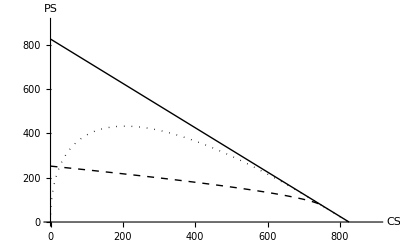

D:\Box Sync\Teaching\Econ 641\Econ 641 - Fall 2017\Lecture notes\quotasefficient.png

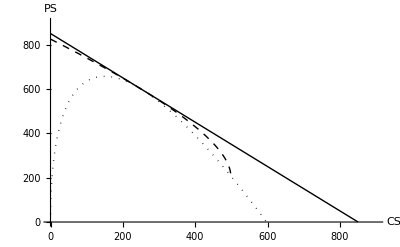

D:\Box Sync\Teaching\Econ 641\Econ 641 - Fall 2017\Lecture notes\subsefficient.png

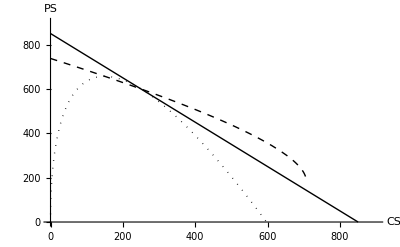

D:\Box Sync\Teaching\Econ 641\Econ 641 - Fall 2017\Lecture notes\costtax.png

```mathematica
Clear["Global`*"]
"Solution Q - Consumer surplus"
QCS=Q/.Solve[CS==Q^2/(2 b),Q][[2]]
"Solution Q - Producer surplus quota"
QPS=Q/.Solve[PS==((a-Q)/b+e/f)Q-1/2*Q^2/f,Q][[2]]
"Solution for Q for subsidy"
Qt=(a f+ b e + b f t)/(b+f)
"Solution t - Producer surplus"
tPS = t/.Flatten[Solve[PS==Qt^2/(2 f),t][[2]]]
"Solution t - consumer surplus and taxation"
tCS=t/.Flatten[Solve[CS==(Qt^2/(2 b)-(1+δ)t*Qt),t][[2]]]
"Calculate parameter values given elasticity"
b=(-η Q0)/P0
a=Q0+b P0
f=(ξ Q0)/P0
e=Q0-f P0
"Calculate max consumers and producers surplus"
CS0=Q0^2/(2 b)
PS0=((a-Q0)/b-(Q0-e)/f)Q0+1/2*Q0^2/f
"Calculate total max surplus"
TS0=CS0+PS0
"Max surplus line"
PSmax = (TS0-CS)
"Surplus transformation curve - Quota"
PScurveQ=Simplify[(PS/.Flatten[Solve[QCS==QPS,PS]])]
"Surplus transformation curve - subsidy"
PScurvet=Simplify[(PS/.Flatten[Solve[(tCS)==tPS,PS]])]
"Graph of surplus transformation curve"
P0=5;Q0=60;
 Manipulate[Plot[{(PSmax/.{η->k, ξ->l}),(PScurveQ/.{η->k, ξ->l}),(PScurvet/.{η->k, ξ->l,δ->j})},{CS,0,1000}, PlotRange->{{0,1000},{0,1000}},AxesLabel->{CS, PS}, PlotStyle -> Thick],{{k,-0.8,"η"},-1,-0.0001},{{l,0.5,"ϵ"},0.0001,3},{{j,0,δ},0,1}]
"Plot for different values of elasticities"
η1=-0.2;ξ1=2;δ1=0;
Plot[{(PSmax/.{η->η1, ξ->ξ1}),(PScurveQ/.{η->η1, ξ->ξ1}),(PScurvet/.{η->η1, ξ->ξ1,δ->δ1})},{CS,0,1000}, PlotRange->{{0,900},{0,900}},AxesLabel->{CS, PS}, PlotStyle -> {Directive[Black,Thick], Directive[Thick,Black,Dotted], Directive[Thick,Dashed,Black] }]
Export["D:\\Box Sync\\Teaching\\Econ 641\\Econ 641 - Fall 2017\\Lecture notes\\quotasefficient.png",%,"png"]
η0=-0.6;ξ0=0.25;δ0=0;
Plot[{(PSmax/.{η->η0, ξ->ξ0}),(PScurveQ/.{η->η0, ξ->ξ0}),(PScurvet/.{η->η0, ξ->ξ0,δ->δ0})},{CS,0,1000}, PlotRange->{{0,900},{0,900}},AxesLabel->{CS, PS}, PlotStyle -> {Directive[Black,Thick], Directive[Thick,Black,Dotted], Directive[Thick,Dashed,Black] }]
Export["D:\\Box Sync\\Teaching\\Econ 641\\Econ 641 - Fall 2017\\Lecture notes\\subsefficient.png",%,"png"]
η2=-0.6;ξ2=0.25;δ2=.5;
Plot[{(PSmax/.{η->η2, ξ->ξ2}),(PScurveQ/.{η->η2, ξ->ξ2}),(PScurvet/.{η->η2, ξ->ξ2,δ->δ2})},{CS,0,1000}, PlotRange->{{0,900},{0,900}},AxesLabel->{CS, PS}, PlotStyle -> {Directive[Black,Thick], Directive[Thick,Black,Dotted], Directive[Thick,Dashed,Black] }]
Export["D:\\Box Sync\\Teaching\\Econ 641\\Econ 641 - Fall 2017\\Lecture notes\\costtax.png",%,"png"]
```

```mathematica
Manipulate[Plot[{PSmax},{CS,0,TS0/.Par}],{P0,5,5},{Q0,60,60},{η,-0.5,-0.5},{ξ,0.8,0.8}]
Plot[{(PSmax/.Par),(PScurve/.Par)},{CS,0,TS0/.Par}]
Plot[{(PSmax/.Par)},{CS,0,TS0/.Par}]
```

√2 √b √CS

(2 b e+2 a f+√((-2 b e-2 a f)^2-8 b f (b+2 f) PS))/(2 (b+2 f))

-(Q0 x)/P0

Q0-Q0 x

(Q0 y)/P0

Q0-Q0 y

-(P0 Q0)/(2 x)

(P0 Q0)/(2 y)

-(P0 Q0)/(2 x)+(P0 Q0)/(2 y)

-CS-(P0 Q0)/(2 x)+(P0 Q0)/(2 y)

(CS x^2+√2 √CS P0 x √(-(Q0 x)/P0)-2 CS x y-√2 √CS P0 √(-(Q0 x)/P0) y)/(x y)

{P0→5,Q0→60,ξ→0.8,η→-0.5}

Plot::plln: Limiting value -150/x + 150/y in {CS, 0, TS0/. Par} is not a machine-size real number.

Plot[{PSmax/.Par,PScurve/.Par},{CS,0,TS0/.Par}]

Plot::plln: Limiting value -150/x + 150/y in {CS, 0, TS0/. Par} is not a machine-size real number.

Plot[{PSmax/.Par},{CS,0,TS0/.Par}]

Plot::plln: Limiting value -150/x + 150/y in {CS, 0, TS0/. Par} is not a machine-size real number.

ReplaceAll::reps: {Par} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value -150/η + 150/ξ/. Par in {CS, 0, TS0/. Par} is not a machine-size real number.

ReplaceAll::reps: {Par} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value -150/η + 150/ξ/. Par in {CS, 0, TS0/. Par} is not a machine-size real number.

ReplaceAll::reps: {Par} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value TS0/. Par in {CS, 0, TS0/. Par} is not a machine-sized real number.

ReplaceAll::reps: {Par} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Plot::plln: Limiting value -150/η + 150/ξ/. Par in {CS, 0, TS0/. Par} is not a machine-sized real number.

√2 √b √CS

(2 b e+2 a f+√((-2 b e-2 a f)^2-8 b f (b+2 f) PS))/(2 (b+2 f))

(-b^(3/2) CS+√2 b √CS e+√2 a √CS f-2 √b CS f)/(√b f)

6.

90.

9.6

12.

300.

187.5

487.5

487.5-CS

0.0425259 (1323.7 √CS-61.7271 CS)

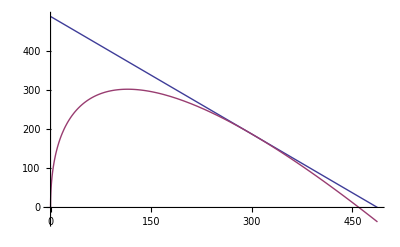

√2 √b √CS

(b+2 b e+2 a f+√((-b-2 b e-2 a f)^2-8 b f (2 b+2 f) PS))/(2 (2 b+2 f))

(√2 b √CS-4 b^(3/2) CS+2 √2 b √CS e+2 √2 a √CS f-4 √b CS f)/(2 √b f)

-(Q0 η)/P0

Q0-(Q0^2 η)/P0

(Q0 ξ)/P0

Q0-Q0 ξ

√2 √B √CS

(CS (1-2 ϵ) η)/ϵ

-0.2

0.6

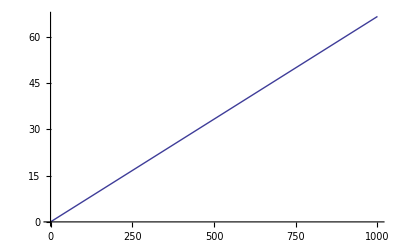

```mathematica
Plot[,{CS,0,TS0}]
```